```mathematica
ClearAll;
```

```mathematica
(*Parameters*)
mu=1.0; (*Solved using constraint on total energy*)
M=1.0;
L=1.0;
z0=0.5;
alpha=0.1; (*Important parameter*)
```

```mathematica
logcosh[x_]:=Module[{s,p},s=Sign[x]*x;
p=Exp[-2*s];
s+Log[1+p]-Log[2]]

H[mu_,ics_,alpha_,z0_,M_]:=Module[{w,z,phi,pw,pz,pphi,L},(*Check if input is a vector (1D case) or matrix (2D case)*)If[VectorQ[ics],(*1D case*){w,z,phi,pw,pz,pphi}=ics,(*2D case (matrix where each row is a phase-space coordinate set)*){w,z,phi,pw,pz,pphi}=Transpose[ics]];
(*Define L in terms of pphi*)L=pphi;
(*Return the energy*)mu*(pw^2/(2*mu)+pz^2/(2*mu)+L^2/(2*mu^2*w^2)-M/Sqrt[w^2+z^2]+alpha*z0*logcosh[z/z0])]
```

```mathematica
(*Initialize ics*)
ics={1.2,0.0,0.0,0.0,0.76,L};

(*Initialize t*)
tspan=Range[0.,100000.,1];
```

```mathematica
(*Define function to evolve the system*)evolve[t_,x_,alpha_]:=Module[{w,z,phi,pw,pz,pphi,dw,dz,dphi,dpw,dpz,dpphi},{w,z,phi,pw,pz,pphi}=x;
(*Calculate derivatives*)
dw=pw;
dz=pz;
dphi=L/(mu*w^2);
dpw=-mu*(-L^2/(mu^2*w^3)+M*w/((w^2+z^2)^(3/2)));
dpz=-mu*(M*z/((w^2+z^2)^(3/2))+alpha*Tanh[z/z0]);
dpphi=0.0;
(*Return result as a list (equivalent to np.array in Python)*){dw,dz,dphi,dpw,dpz,dpphi}];
```

```mathematica
(*Solve the differential equation system*){sol,pointsData}=Reap@NDSolve[{(*System of differential equations*)Thread[D[{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},t]==evolve[t,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha]],(*Initial conditions*)w[0]==ics[[1]],z[0]==ics[[2]],phi[0]==ics[[3]],pw[0]==ics[[4]],pz[0]==ics[[5]],pphi[0]==ics[[6]],(*Poincare section condition*)WhenEvent[z[t]==0 && pz[t]>0,Sow[{w[t],pw[t],H[mu,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha,z0,M]}]]},{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},{t,0,tspan[[-1]]},Method->{"StiffnessSwitching"},AccuracyGoal->11,PrecisionGoal->11];
```

```mathematica
points= pointsData[[1,All,{1,2}]]
```

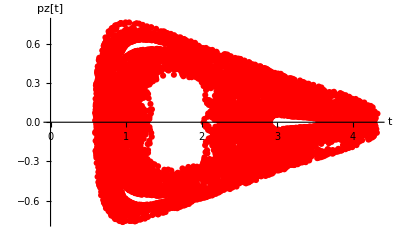

```mathematica
(*Plot the points*)ListPlot[points,PlotStyle->Red,PlotLegends->"Expressions",AxesLabel->{"t","pz[t]"},PlotMarkers->Automatic]
```

```mathematica
Energy=pointsData[[1,All,3]];
```

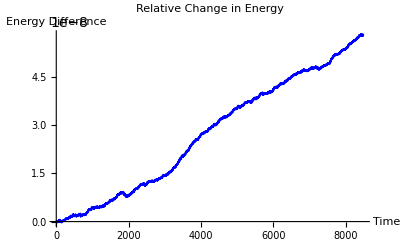

```mathematica
(*Line plot*)ListLinePlot[Energy-Energy[[1]],PlotStyle->Blue,AxesLabel->{"Time","Energy Difference"},PlotLabel->"Relative Change in Energy"]
```

```mathematica
Clear[t,usol,X1t,w,z,pw,pz,pphi,dw,dz,dphi,dpw,dpz,dpphi];
(*Define the chaotic_lyp function in Mathematica*)chaoticLyp[t_,Y_,alpha_]:=Module[{w,z,phi,pw,pz,pphi,dfw,dfz,dfphi,dfpw,dfpz,dfpphi,dfhdwdw,dfhdwdz,dfhdzdz,J,dY,dYdt},(*Unpack Y*){w,z,phi,pw,pz,pphi}=Take[Y,6];
(*System of differential equations*)
dfw=pw;
dfz=pz;
dfphi=L/(mu*w^2);
dfpw=-mu*(-L^2/(mu^2*w^3)+M*w/((w^2+z^2)^(3/2)));
dfpz=-mu*(M*z/((w^2+z^2)^(3/2))+alpha*Tanh[z/z0]);
dfpphi=0.0;
(*Jacobian matrix elements*)
dfhdwdw=-mu*(3*L^2/((mu^2)*(w^4))-3*M*w^2/((w^2+z^2)^(5/2))+M/((w^2+z^2)^(3/2)));
dfhdwdz=3*M*mu*w*z/((w^2+z^2)^(5/2));
dfhdzdz=-mu*(-3*M*z^2/((w^2+z^2)^(5/2))+M/((w^2+z^2)^(3/2))+alpha*(Sech[z/z0]^2)/z0);
(*Jacobian matrix*)J={{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{-2.*L/(mu*w^3.),0.,0.,0.,0.,1./(mu*w^2.)},{dfhdwdw,dfhdwdz,0.,0.,0.,2.*L/(mu*w^3.)},{dfhdwdz,dfhdzdz,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}};
(*Extract dY and reshape*)
dY=ArrayReshape[Drop[Y,6],{6,1}];
(*Compute dY_dt*)
dYdt=J.dY;
(*Concatenate the results and return the final output*)
Join[{dfw,dfz,dfphi,dfpw,dfpz,dfpphi},Flatten[dYdt]]]
```

```mathematica
(*Example initial conditions and time*)
ics={1.2,0.0,0.0,0.0,0.76,L};  
(*Generate random normal values for w(0)*)
w0=RandomVariate[NormalDistribution[0,1],6];
(*Normalize w(0) to make it a unitary vector*)
w0=w0/Norm[w0];
(*Combine u0 and w0 into a single flattened vector*)
Y0=Flatten[{ics,w0}]
(*Call the chaoticLyp function*)
chaoticLyp[t,Y0,alpha]
```

{1.2,0.,0.,0.,0.76,1.,0.546712,0.224916,-0.623405,0.194887,0.0900252,-0.464543}

{0.,0.76,0.694444,-0.115741,0.,0.,0.194887,0.0900252,-0.955367,-0.695857,-0.175143,0.}

```mathematica
Clear[t,usol,X1t,w,z,pw,pz,pphi,dw,dz,dphi,dpw,dpz,dpphi];
(* Get the Lyapunov Exponent of the trajectory*)
tau=1000;
{usol,X1t}=Reap@NDSolve[{Thread[D[{w[t],z[t],phi[t],pw[t],pz[t],pphi[t],dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]},t]==chaoticLyp[t,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t],dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]},alpha]],(*Initial conditions*)w[0]==Y0[[1]],z[0]==Y0[[2]],phi[0]==Y0[[3]],pw[0]==Y0[[4]],pz[0]==Y0[[5]],pphi[0]==Y0[[6]],dw[0]==Y0[[7]],dz[0]==Y0[[8]],dphi[0]==Y0[[9]],dpw[0]==Y0[[10]],dpz[0]==Y0[[11]],dpphi[0]==Y0[[12]],WhenEvent[Mod[t,tau]==0,{Sow[{Log[Norm[{dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]}]],H[mu,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha,z0,M]}],{dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]}->{dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]}/Norm[{dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]}]}]},{w[t],z[t],phi[t],pw[t],pz[t],pphi[t],dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]},{t,0.,100000.},Method->{"StiffnessSwitching"},AccuracyGoal->12,PrecisionGoal->12];
```

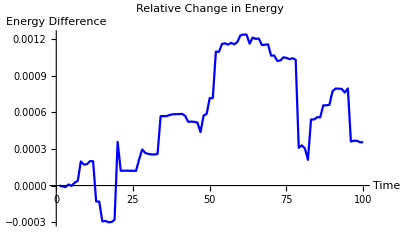

```mathematica
ListLinePlot[X1t[[1,All,2]]-X1t[[1,All,2]][[1]],PlotStyle->Blue,AxesLabel->{"Time","Energy Difference"},PlotLabel->"Relative Change in Energy"]
```

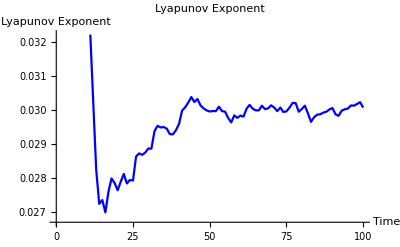

```mathematica
ListLinePlot[Accumulate[X1t[[1,All,1]]]/Range[tau,100000.,tau],PlotStyle->Blue,AxesLabel->{"Time","Lyapunov Exponent"},PlotLabel->"Lyapunov Exponent"]
```

```mathematica
Thread[D[{w[t],z[t],phi[t],pw[t],pz[t],pphi[t],dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]},t]==chaoticLyp[t,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t],dw[t],dz[t],dphi[t],dpw[t],dpz[t],dpphi[t]},alpha]]
```

{w'[t]==pw[t],z'[t]==pz[t],phi'[t]==1./w[t]^2,pw'[t]==-1. (-1./w[t]^3+(1. w[t])/((w[t]^2+z[t]^2)^(3/2))),pz'[t]==-1. (0.1 Tanh[2. z[t]]+(1. z[t])/((w[t]^2+z[t]^2)^(3/2))),pphi'[t]==0.,dw'[t]==0.+1. dpw[t],dz'[t]==0.+1. dpz[t],dphi'[t]==0.-(2. dw[t])/w[t]^3.+(1. dpphi[t])/w[t]^2.,dpw'[t]==0.+(2. dpphi[t])/w[t]^3.+(3. dz[t] w[t] z[t])/((w[t]^2+z[t]^2)^(5/2))-1. dw[t] (3./w[t]^4-(3. w[t]^2)/((w[t]^2+z[t]^2)^(5/2))+1./((w[t]^2+z[t]^2)^(3/2))),dpz'[t]==0.+(3. dw[t] w[t] z[t])/((w[t]^2+z[t]^2)^(5/2))-1. dz[t] (0.2 Sech[2. z[t]]^2-(3. z[t]^2)/((w[t]^2+z[t]^2)^(5/2))+1./((w[t]^2+z[t]^2)^(3/2))),dpphi'[t]==0.}